## Set up the models and the standard parameters

The goal here is to re-connect the ideas of the models and the parameters we had before to try and think about some implied landscape where we can see what the distribution is of the probability that some organisms will end up using the same space on a landscape.

```mathematica
(*Define constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;

(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*adjust for larger or smaller landscapes*)

(*Generate random values for T and S across the grid*)
meanT = 20;
varT = 5;
alphaS = 1.2;
betaS = 1;
Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[GammaDistribution[alphaS,betaS],gridSize];

(*Compute probabilities w_{i,j} across the landscape*)
(*Truncate landscape probabilities to be>=0*)
landscapeProbabilities=Table[Max[0,w[Tgrid[[i,j]],Sgrid[[i,j]]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];
```

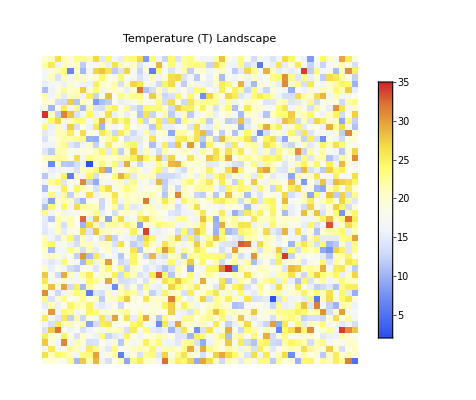
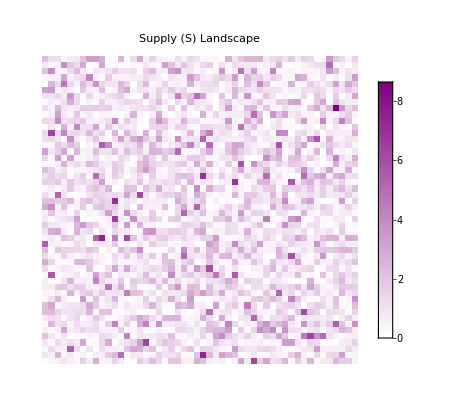
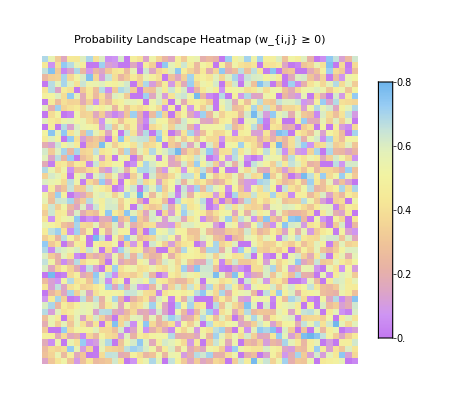
-Graphics- | -Graphics-
 | -Graphics-

```mathematica
(*Heatmap for w_{i,j} values with Magma color scheme*)heatmapW=ArrayPlot[landscapeProbabilities,ColorFunction->"Pastel",Mesh->False,PlotLabel->"Probability Landscape Heatmap (w_{i,j} ≥ 0)",PlotLegends->Automatic];

(*Heatmap for T values with TemperatureMap color scheme*)
heatmapT=ArrayPlot[Tgrid,ColorFunction->"TemperatureMap",Mesh->False,PlotLabel->"Temperature (T) Landscape",PlotLegends->Automatic];

(*Heatmap for S values with purple gradient color scheme*)
heatmapS=ArrayPlot[Sgrid,ColorFunction->(Blend[{White,Purple},#]&),Mesh->False,PlotLabel->"Supply (S) Landscape",PlotLegends->Automatic];


(*Arrange the plots in a grid with T and S on the top row,w at double size on the second row*)Grid[{{heatmapT,heatmapS},{SpanFromLeft,heatmapW}},Spacings->{2,1}]
```

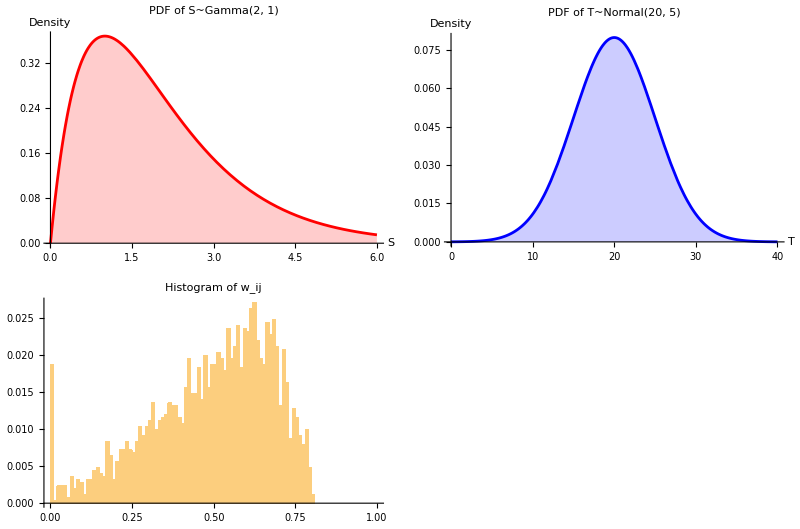

```mathematica
(*Flatten the landscape probabilities for density plot*)
flatProbabilities=Flatten[landscapeProbabilities];

(*Plot as a density plot*)
pdfPlotS=Plot[PDF[GammaDistribution[alphaS,betaS],x],{x,0,6},PlotLabel->Style[Text@StringJoin["PDF of S~Gamma(",ToString[alphaS],", ",ToString[betaS],")"],14],Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},PlotLabel->Style[Text@StringJoin["PDF of T~Normal(",ToString[meanT],", ",ToString[varT],")"],14],Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
hist=Histogram[flatProbabilities,{0, 1, 0.01},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of w_ij"],14]];

(*Display all three plots*)
GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist}},Spacings->{1,2}]
```

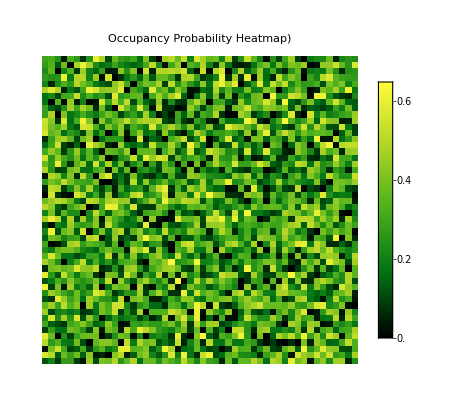

```mathematica
(*Calculate the probability that two organisms occupy the same place*)
occupancyProbability=landscapeProbabilities^2;
heatmapO=ArrayPlot[occupancyProbability,ColorFunction->"AvocadoColors",Mesh->False,PlotLabel->"Occupancy Probability Heatmap)",PlotLegends->Automatic];
heatmapO
```

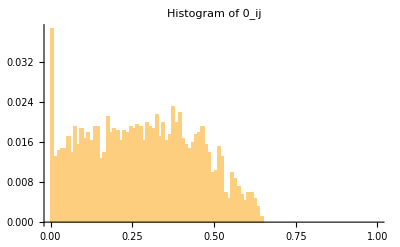

```mathematica
histO=Histogram[Flatten[occupancyProbability],{0, 1, 0.01},"Probability",PlotLabel->Style[Text@StringJoin["Histogram of 0_ij"],14]];
histO
```

```mathematica
Total[Total[Flatten[occupancyProbability]]] //Timing
50 * 50
```

{0.000627,699.261}

2500

Notes: 
- next i’ll want to parallelize (do-loop etc) to get to values of C 
	- will automatically localize variables within a loop -- you can globalize it -- SetSharedVariable[] which will then allow you to write that variable outside 
	- if you use the command parallel table, it will collect your data for you automatically 
	ParallelTable[ 
	...
	....
	...
	
	{muT, sigmaT, C}
	], {ranges of muT, sigmaT etc etc} 
	- for this, we’ll have to figure out where to cut it off such that you have ALL of your cells with zero fitness, safeguard against division by zero here 
	- we’re imaginging it on a grid but we don’t need to do that we could just take 10,000 samples and try to characterize the surfaces of that “bowl” for T -- leave S alone for now 
	
- for moving from 2 individuals and 50 cells, to whatever number of each -- if you’re calculating C, you’re actually calculating it per-patch, so you can say that each pair of infectives and susceptibles in the system has the value C, so there should be some way to calculate for any number I and S, how many possible pairings there are and then get some probability from there that scales up 

\begin{equation}
...
\end{}

β_(i j)